## Maximum Coupled Entropy Principle

### Maximum Coupled Entropy

Use of Lagrange Method to determine one-dimensional Maximum Entropy distribution

```mathematica
$Assumptions=n∈PositiveIntegers&&{κ,α,σ,μ,ZP,λ,W,x}∈Reals&&0<κ<∞&&0<α<∞&&0<σ<∞&&0<μ<∞&&0<ZP<∞&&0<λ<∞&&0<W<∞;
```

```mathematica
(*P[κ_,α_,n_]:=Table[Subscript[p, i]^(1+(α κ)/(1+κ)),{i,1,n}]/(∑_(i=1)^n Subscript[p, i]^(1+(α κ)/(1+κ)));*)
P[κ_,α_,n_]:=Table[Subscript[p, i]^(1+(α κ)/(1+κ)),{i,1,n}]/ZP;
```

Investigation clarified that α is determined by the highest power of the constraint. Given a requirement that the coupled entropy converge to the Shannon entropy for κ→0 and all α a multiplier by 1/αis needed for both the entropy and the constraint. This investigation is limited to just two constraints, the sum of probabilities is one, and one of the coupled moments.

```mathematica
ϕ[κ_,α_,σ_,n_]:=
1/(α κ)(∑_(i=1)^n P[κ,α,n]_⟦i⟧((Subscript[p, i])^((-α κ)/(1+κ))-1))+∑_(i=1)^n Subscript[p, i]-1/σ∑_(i=1)^n P[κ,α,n]_⟦i⟧Subscript[x, i]
```

```mathematica
Solve[D[ϕ[κ,1,σ,3],Subscript[p, 1]]==0,Subscript[p, 1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p_1→(((1+κ) (1+ZP κ) σ)/((1+2 κ) (σ+κ x_1)))^((1+κ)/κ)}}

```mathematica
{{Subscript[p, 1]->(((1+2 κ) (1+κ Subscript[x, 1]/σ))/((1+κ) (1+2 ZP κ)))^((1+κ)/-κ)}}
```

If x_i=i-1, then ZP is (however, unable to solve since ZP is part of solution)

```mathematica
ZP=∑_(i=1)^3 ((((1+2 κ) (1+κ (i-1)/σ))/((1+κ) (1+2 ZP κ)))^((1+κ)/-κ))^(1+κ/(1+κ))//FullSimplify
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ((1+2 κ)/((1+κ) (1+2 ZP κ)))^(-2-1/κ).

Hold[((1+2 κ)/((1+κ) (1+2 ZP κ)))^(-2-1/κ)+(((1+2 κ) (κ+σ))/((1+κ) (1+2 ZP κ) σ))^(-2-1/κ)+(((1+2 κ) (2 κ+σ))/((1+κ) (1+2 ZP κ) σ))^(-2-1/κ)]

But given the structure of the solution, can determine the normalization

```mathematica
∑_(i=1)^3 (1+κ (i-1)/σ)^((1+κ)/-κ)//FullSimplify
```

1+(1+(2 κ)/σ)^(-(1+κ)/κ)+((κ+σ)/σ)^(-(1+κ)/κ)

```mathematica
(1+(1+(2 κ)/σ)^(-(1+κ)/κ)+((κ+σ)/σ)^(-(1+κ)/κ))^-1 (1+κ Subscript[x, i]/σ)^((1+κ)/-κ)//FullSimplify
```

(1+(κ x_i)/σ)^(-(1+κ)/κ)/(1+(1+(2 κ)/σ)^(-(1+κ)/κ)+((κ+σ)/σ)^(-(1+κ)/κ))

#### Solution for α = 2 with Coupled Variance Constraint

In order to ensure that the correct form of the probability is achieved, either
1) the 1/2needs to be removed from the coupled entropy, or
2) a 1/2needs to multiply the coupled variance constraint term

```mathematica
D[ϕ[κ,2,σ,3]]//FullSimplify
```

((σ+2 ZP κ σ) p_1+(σ+2 ZP κ σ) p_2-p_1^(1+(2 κ)/(1+κ)) (σ+2 κ x_1)-p_2^(1+(2 κ)/(1+κ)) (σ+2 κ x_2)+p_3 (σ+2 ZP κ σ-p_3^((2 κ)/(1+κ)) (σ+2 κ x_3)))/(2 ZP κ σ)

```mathematica
Solve[D[ϕ[κ,2,σ,3],Subscript[p, 1]]==0,Subscript[p, 1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p_1→(-(√(1+κ) √(1+2 ZP κ) √σ)/(√(σ+3 κ σ+2 κ x_1+6 κ^2 x_1)))^((1+κ)/κ)},{p_1→((√(1+κ) √(1+2 ZP κ) √σ)/(√(σ+3 κ σ+2 κ x_1+6 κ^2 x_1)))^((1+κ)/κ)}}

```mathematica
1/((√(1+κ) √(1+ZP κ) σ)/(√(σ^2+3 κ σ^2+κ Subscript[x, 1]^2+3 κ^2 Subscript[x, 1]^2)))//FullSimplify
```

(√(((1+3 κ) (σ^2+κ x_1^2))/((1+κ) (1+ZP κ))))/σ

```mathematica
Subscript[p, i]->1/Z(1+ κ Subscript[x, i]^2/σ^2)^((1+κ)/(-2κ))
```

So indeed the factor of 2 division causes a problem in correctly specifying the coupled variance constraint; however, I next need to examine whether the entropy function should change or the constraint should change.

#### Solution for α with α constraint

```mathematica
ϕAlpha[κ_,α_,σ_,n_]:=
1/(α κ)(∑_(i=1)^n P[κ,α,n]_⟦i⟧((Subscript[p, i])^((-α κ)/(1+κ))-1))+∑_(i=1)^n Subscript[p, i]-1/(α σ^α)∑_(i=1)^n P[κ,α,n]_⟦i⟧(Subscript[x, i]-μ)^α;
```

```mathematica
D[ϕAlpha[κ,α,σ,3],Subscript[p, 1]]//FullSimplify
```

(σ^-α ((1+κ) (1+ZP α κ) σ^α-(1+κ+α κ) p_1^((α κ)/(1+κ)) (σ^α+κ (-μ+x_1)^α)))/(ZP α κ (1+κ))

```mathematica
Solve[(σ^-α ((1+κ) (1+ZP α κ) σ^α-(1+κ+α κ) Subscript[p, 1]^((α κ)/(1+κ)) (σ^α+κ (-μ+Subscript[x, 1])^α)))/(ZP α κ (1+κ))==0,Subscript[p, 1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p_1→(((1+κ) (1+ZP α κ) σ^α)/((1+κ+α κ) (σ^α+κ (-μ+x_1)^α)))^((1+κ)/(α κ))}}

p_1=1/Z(1+κ(-μ+x_1)^α/σ^α)^((1+κ)/(-α κ)) =1/Z((1+κ(-μ+x_1)^α/σ^α)^(1/κ))^((1+κ)/-α)=1/Z exp_κ^(-(1+κ)/α)((-μ+x_1)^α/σ^α)

### Scaling Properties of Coupled Entropy

Hanel, Thurner have written a series of papers on the broadest generalization of entropies relaxing the assumption of additivity. They formulated a c,d-entropy in which c and d relate to different scaling properties of the generalized entropy. The parameter c is equal to Tsallis’ q parameter, and thus c=q=1+(α κ)/(1+d κ). The parameter d  relates to raising the generalized logarithm to a power. Following the scaling derivation in R. Hanel and S. Thurner, “A classification of complex statistical systems in terms of their stability and a thermodynamical derivation of their entropy and distribution functions,” 2010., we have the following properties for the Coupled Entropy.

```mathematica
FullSimplify[λ(1/(λ W)(1/-2)CoupledLogarithm[(1/(λ W))^-2,κ,1])/(1/W(1/-2)CoupledLogarithm[(1/W)^-2,κ,1])]
```

(-1+(W λ)^((2 κ)/(1+κ)))/(-1+W^((2 κ)/(1+κ)))

```mathematica
Limit[(-1+(W λ)^((2 κ)/(1+κ)))/(-1+W^((2 κ)/(1+κ))),W->∞]
```

λ^((2 κ)/(1+κ))

As 0≤κ≤∞, the scaling ranges from 0≤(2 κ)/(1+κ)≤1 which is consistent with the specifications given by Hanel, Thurner. Also note, that -1≤κ<0 the scaling is faster than exponential and could be governed by the κ = 0 case. If we solve for c, we have c=1-(2 κ)/(1+κ), which is not q. Rather c=1-(-1+q)=2+q and q=c-2. This seems inconsistent in that for 0<c≤1, then -2<q≤-1. There must be another transformation, for instance the Q=2-q, which switches the domains of q. Substituting q→2-Q, gives c=4-Q, which is not helpful, but if c→2-Q, then have q=-Q.  If we take the relationship to be c=2-Q, then for 0<c≤1, 2>Q≥1. This leaves out the domain 2<Q<3; however, it is closer to the intent of the heavy-tail scaling.

## Examination of the Coupled Entropy with a Root

Examination clarified that the root has a different role than α. 
None of these examinations resulted in an equation that “Solve” could provide a solution.
Following Tsallis’ notation the symbol for the root is suggested to δ.

#### Solution for α = 1 with Mean Constraint and a root expression for the entropy

```mathematica
ϕRootMean[κ_,σ_,n_]:=
1/(√κ)(∑_(i=1)^n P[κ,1,n]_⟦i⟧((Subscript[p, i])^((- κ)/(1+κ))-1)^(1/2))+∑_(i=1)^n Subscript[p, i]-1/σ∑_(i=1)^n P[κ,1,n]_⟦i⟧Subscript[x, i]
```

```mathematica
D[ϕRootMean[κ,σ,3],Subscript[p, 1]]//FullSimplify
```

1+(2+3 κ-2 (1+2 κ) p_1^(κ/(1+κ)))/(2 ZP (1+κ) √(κ (-1+p_1^(-1+1/(1+κ)))))-((1+κ/(1+κ)) p_1^(κ/(1+κ)) x_1)/(ZP σ)

```mathematica
Solve[1+(2+3 κ-2 (1+2 κ) Subscript[p, 1]^(κ/(1+κ)))/(2 ZP (1+κ) √(κ (-1+Subscript[p, 1]^(-1+1/(1+κ)))))-((1+κ/(1+κ)) Subscript[p, 1]^(κ/(1+κ)) Subscript[x, 1])/(ZP σ)==0,Subscript[p, 1]]//FullSimplify
```

$Aborted

Aborted after approximately 1-2 hours

#### Solution for α = 2 with Coupled Variance Constraint and a root expression for the entropy

Below used root entropy with a second moment constraint. With the root 1/2, this is equivalent to having a higher moment constraint if the derivative is squared.

```mathematica
ϕRoot[κ_,σ_,n_]:=
1/(√κ)(∑_(i=1)^n P[κ,2,n]_⟦i⟧((Subscript[p, i])^((-2 κ)/(1+κ))-1)^(1/2))+∑_(i=1)^n Subscript[p, i]-1/σ^2∑_(i=1)^n P[κ,2,n]_⟦i⟧Subscript[x, i]^2
```

```mathematica
D[ϕRoot[κ,σ,3],Subscript[p, 1]]//FullSimplify
```

1+(1+2 κ-(1+3 κ) p_1^((2 κ)/(1+κ)))/(ZP (1+κ) √(κ (-1+p_1^(-(2 κ)/(1+κ)))))-((1+3 κ) p_1^((2 κ)/(1+κ)) x_1^2)/(ZP (1+κ) σ^2)

```mathematica
Solve[1+(1+2 κ-(1+3 κ) Subscript[p, 1]^((2 κ)/(1+κ)))/(ZP (1+κ) √(κ (-1+Subscript[p, 1]^(-(2 κ)/(1+κ)))))-((1+3 κ) Subscript[p, 1]^((2 κ)/(1+κ)) Subscript[x, 1]^2)/(ZP (1+κ) σ^2)==0,Subscript[p, 1]]//FullSimplify
```

$Aborted

Above did not find a solution within 3 hours of processing. Try squaring to see if this will simplify the expression

```mathematica
(1+(1+2 κ-(1+3 κ) Subscript[p, 1]^((2 κ)/(1+κ)))/(ZP (1+κ) √(κ (-1+Subscript[p, 1]^(-(2 κ)/(1+κ)))))-((1+3 κ) Subscript[p, 1]^((2 κ)/(1+κ)) Subscript[x, 1]^2)/(ZP (1+κ) σ^2))^2//Expand
```

1+4/(ZP^2 (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))+1/(ZP^2 κ (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))+(4 κ)/(ZP^2 (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))-(10 p_1^((2 κ)/(1+κ)))/(ZP^2 (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))-(2 p_1^((2 κ)/(1+κ)))/(ZP^2 κ (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))-(12 κ p_1^((2 κ)/(1+κ)))/(ZP^2 (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))+(6 p_1^((4 κ)/(1+κ)))/(ZP^2 (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))+p_1^((4 κ)/(1+κ))/(ZP^2 κ (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))+(9 κ p_1^((4 κ)/(1+κ)))/(ZP^2 (1+κ)^2 (-1+p_1^(-(2 κ)/(1+κ))))+(4 √(κ (-1+p_1^(-(2 κ)/(1+κ)))))/(ZP (1+κ) (-1+p_1^(-(2 κ)/(1+κ))))+(2 √(κ (-1+p_1^(-(2 κ)/(1+κ)))))/(ZP κ (1+κ) (-1+p_1^(-(2 κ)/(1+κ))))-(6 p_1^((2 κ)/(1+κ)) √(κ (-1+p_1^(-(2 κ)/(1+κ)))))/(ZP (1+κ) (-1+p_1^(-(2 κ)/(1+κ))))-(2 p_1^((2 κ)/(1+κ)) √(κ (-1+p_1^(-(2 κ)/(1+κ)))))/(ZP κ (1+κ) (-1+p_1^(-(2 κ)/(1+κ))))-(2 p_1^((2 κ)/(1+κ)) x_1^2)/(ZP (1+κ) σ^2)-(6 κ p_1^((2 κ)/(1+κ)) x_1^2)/(ZP (1+κ) σ^2)-(10 p_1^((2 κ)/(1+κ)) √(κ (-1+p_1^(-(2 κ)/(1+κ)))) x_1^2)/(ZP^2 (1+κ)^2 σ^2 (-1+p_1^(-(2 κ)/(1+κ))))-(2 p_1^((2 κ)/(1+κ)) √(κ (-1+p_1^(-(2 κ)/(1+κ)))) x_1^2)/(ZP^2 κ (1+κ)^2 σ^2 (-1+p_1^(-(2 κ)/(1+κ))))-(12 κ p_1^((2 κ)/(1+κ)) √(κ (-1+p_1^(-(2 κ)/(1+κ)))) x_1^2)/(ZP^2 (1+κ)^2 σ^2 (-1+p_1^(-(2 κ)/(1+κ))))+(12 p_1^((4 κ)/(1+κ)) √(κ (-1+p_1^(-(2 κ)/(1+κ)))) x_1^2)/(ZP^2 (1+κ)^2 σ^2 (-1+p_1^(-(2 κ)/(1+κ))))+(2 p_1^((4 κ)/(1+κ)) √(κ (-1+p_1^(-(2 κ)/(1+κ)))) x_1^2)/(ZP^2 κ (1+κ)^2 σ^2 (-1+p_1^(-(2 κ)/(1+κ))))+(18 κ p_1^((4 κ)/(1+κ)) √(κ (-1+p_1^(-(2 κ)/(1+κ)))) x_1^2)/(ZP^2 (1+κ)^2 σ^2 (-1+p_1^(-(2 κ)/(1+κ))))+(p_1^((4 κ)/(1+κ)) x_1^4)/(ZP^2 (1+κ)^2 σ^4)+(6 κ p_1^((4 κ)/(1+κ)) x_1^4)/(ZP^2 (1+κ)^2 σ^4)+(9 κ^2 p_1^((4 κ)/(1+κ)) x_1^4)/(ZP^2 (1+κ)^2 σ^4)

```mathematica
%78//FullSimplify
```

1/(ZP^2 κ (1+κ)^2 σ^4 (-1+p_1^((2 κ)/(1+κ))))(-ZP^2 κ (1+κ)^2 σ^4+p_1^((2 κ)/(1+κ)) ((-1+κ (1+κ) (-4+ZP^2 (1+κ))) σ^4+2 ZP (1+κ) σ^2 (-(1+2 κ) σ^2 √(κ (-1+p_1^(-(2 κ)/(1+κ))))+κ (1+3 κ) x_1^2)+(1+3 κ)^2 p_1^((4 κ)/(1+κ)) (-σ^4-2 σ^2 √(κ (-1+p_1^(-(2 κ)/(1+κ)))) x_1^2+κ x_1^4)+(1+3 κ) p_1^((2 κ)/(1+κ)) (2 σ^4 (1+ZP √(κ (-1+p_1^(-(2 κ)/(1+κ))))+κ (2+ZP √(κ (-1+p_1^(-(2 κ)/(1+κ))))))+2 σ^2 (-ZP κ (1+κ)+(1+2 κ) √(κ (-1+p_1^(-(2 κ)/(1+κ))))) x_1^2-κ (1+3 κ) x_1^4)))

```mathematica
Solve[%79==0,Subscript[p, 1]]
```

$Aborted

#### Hanel, Thurner c,d entropy

#### Simplification of Hanel, Thurner solution for α = 2 assuming that c = 1 +(α κ)/(1+κ), d = α

Choose ProductLog branch with k = 0 which covers d >= 0, and subsitute

```mathematica
Clear[HTMaxEntDist,B,r];
HTMaxEntDist[x_,c_,d_]:=Exp[-d/(1-c)(ProductLog[B[c,d](1-x/r[c,d])^(1/d)]-ProductLog[B[c,d]])];
B[c_,d_]:=((1-c)r[c,d])/(1-(1-c)r[c,d])Exp[((1-c)r[c,d])/(1-(1-c)r[c,d])];
r[c_,d_]:=(1-c+c d)^-1;
```

Solve for the case of α = 1

```mathematica
HTMaxEntDist[-x,1+κ/(1+κ),1]//FullSimplify
```

ⅇ^((1+κ) (1/(1+2 κ)+ProductLog[-(ⅇ^(-κ/(1+2 κ)) (1+x) κ)/(1+2 κ)]/κ))

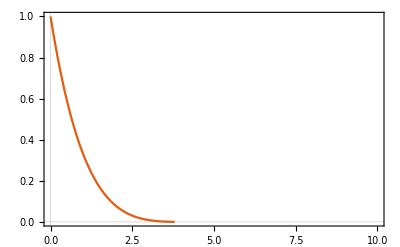

```mathematica
Plot[HTMaxEntDist[-x,1+κ/(1+κ),1]/.{κ->0.1,κ->0.5,κ->1}//Evaluate,
{x,0,10},
PlotTheme->"Scientific"
]
```

Can the Cauchy Distribution be obtained from c = 2, d = 2

```mathematica
HTMaxEntDist[-x,2,2]//FullSimplify
```

ⅇ^(1/2+2 ProductLog[-(√(1+3 x))/(4 ⅇ^(1/4))])

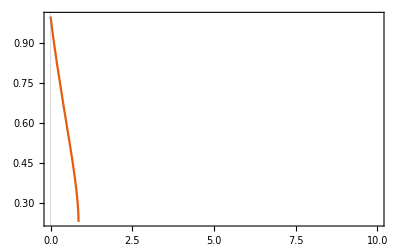

```mathematica
Plot[HTMaxEntDist[-x,2,2]/.{κ->0.1,κ->0.5,κ->1}//Evaluate,
{x,0,10},
PlotTheme->"Scientific"
]
```

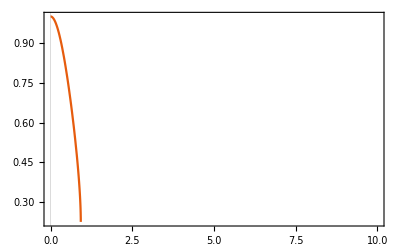

```mathematica
Plot[HTMaxEntDist[-x^2,2,2]/.{κ->0.1,κ->0.5,κ->1}//Evaluate,
{x,0,10},
PlotTheme->"Scientific"
]
```

```mathematica
Limit[(1 + κ x)^((1+κ)/κ),κ->0]
```

ⅇ^x

```mathematica
Limit[(1 + κ x)^(1/κ)(1 + κ x)^d,κ->0]
```

ⅇ^x

```mathematica
Reduce[D[ϕ[κ,1,σ,3],Subscript[p, 1]]==0,Subscript[p, 1]]
```

$Aborted

```mathematica
α^2+σ^2//FullSimplify
```

α^2+σ^2

```mathematica
(
```

## Investigation of Alternative Forms of Coupled Entropy and its Constraints

#### If entropy is set with α = 1 but the second moment constraint is included

```mathematica
ϕAlt[κ_,σ_,n_]:=
1/κ(∑_(i=1)^n P[κ,1,n]_⟦i⟧((Subscript[p, i])^((- κ)/(1+κ))-1))+∑_(i=1)^n Subscript[p, i]-1/σ^2∑_(i=1)^n P[κ,1,n]_⟦i⟧Subscript[x, i]^2
```

```mathematica
D[ϕAlt[κ,σ,3],Subscript[p, 1]]//FullSimplify
```

((1+κ) (1+ZP κ) σ^2-(1+2 κ) p_1^(κ/(1+κ)) (σ^2+κ x_1^2))/(ZP κ (1+κ) σ^2)

```mathematica
Solve[((1+κ) (1+ZP κ) σ^2-(1+2 κ) Subscript[p, 1]^(κ/(1+κ)) (σ^2+κ Subscript[x, 1]^2))/(ZP κ (1+κ) σ^2)==0,Subscript[p, 1]]
```

{{p_1→(((1+κ) (1+ZP κ) σ^2)/((1+2 κ) (σ^2+κ x_1^2)))^((1+κ)/κ)}}

```mathematica
{{Subscript[p, 1]->(((1+2 κ) (1+κ Subscript[x, 1]^2/σ^2))/((1+κ) (1+ZP κ)))^((1+κ)/-κ)}}
```

So the form is a coupled Gaussian but it is missing the 1/2 in the exponent and thus κ is no longer the shape of the distribution

```mathematica
ϕAlt[κ_,σ_,n_]:=
1/κ(∑_(i=1)^n P[κ,2,n]_⟦i⟧((Subscript[p, i])^((- 2κ)/(1+κ))-1))+∑_(i=1)^n Subscript[p, i]-1/σ^2∑_(i=1)^n P[κ,2,n]_⟦i⟧Subscript[x, i]^2
```

```mathematica
D[ϕAlt[κ,σ,3],Subscript[p, 1]]//FullSimplify
```

((1+κ) (1+ZP κ) σ^2-(1+3 κ) p_1^((2 κ)/(1+κ)) (σ^2+κ x_1^2))/(ZP κ (1+κ) σ^2)

```mathematica
Solve[((1+κ) (1+ZP κ) σ^2-(1+3 κ) Subscript[p, 1]^((2 κ)/(1+κ)) (σ^2+κ Subscript[x, 1]^2))/(ZP κ (1+κ) σ^2)==0,Subscript[p, 1]]//FullSimplify
```

{{p_1→(-(√((1+κ) (1+ZP κ)) σ)/(√((1+3 κ) (σ^2+κ x_1^2))))^(1+1/κ)},{p_1→((√((1+κ) (1+ZP κ)) σ)/(√((1+3 κ) (σ^2+κ x_1^2))))^(1+1/κ)}}

```mathematica
{Subscript[p, 1]->(((1+3 κ) (1+κ Subscript[x, 1]^2/σ^2))/((1+κ) (1+ZP κ)))^((1+κ)/(-2κ))}
```

So the 1/2 multiple is not strictly necessary to achieve the coupled Gaussian form; however, in this case the coupled entropy doesn’t converge to the Shannon entropy for κ→0

```mathematica
Limit[(P[κ,2,3]_⟦1⟧((Subscript[p, 1])^((- 2κ)/(1+κ))-1))/κ,κ->0]
```

-(2 Log[p_1] p_1)/ZP

```mathematica
ϕAlt[0,σ_,n_]:=
-∑_(i=1)^n (2 Log[Subscript[p, i]] Subscript[p, i])/ZP+∑_(i=1)^n Subscript[p, i]-1/σ^2∑_(i=1)^n Subscript[p, i] Subscript[x, i]^2
```

```mathematica
D[ϕAlt[0,σ,3],Subscript[p, 1]]//FullSimplify
```

(-2+ZP-2 Log[p_1])/ZP-x_1^2/σ^2

```mathematica
Solve[(-2+ZP-2 Log[Subscript[p, 1]])/ZP-Subscript[x, 1]^2/σ^2==0,Subscript[p, 1]]//FullSimplify
```

{{p_1→ConditionalExpression[ⅇ^(1/2 (-2+ZP-(ZP x_1^2)/σ^2)), -2 π≤(ZP Im[x_1^2])/σ^2<2 π]}}

Alternatively if the entropy is divided by 2

```mathematica
ϕAlt2[0,σ_,n_]:=
-∑_(i=1)^n (Log[Subscript[p, i]] Subscript[p, i])/ZP+∑_(i=1)^n Subscript[p, i]-1/σ^2∑_(i=1)^n Subscript[p, i] Subscript[x, i]^2
```

```mathematica
Solve[D[ϕAlt[0,σ,3],Subscript[p, 1]]-Subscript[x, 1]^2/σ^2==0,Subscript[p, 1]]//FullSimplify
```

{{p_1→ConditionalExpression[ⅇ^(-1+ZP/2-(ZP x_1^2)/σ^2), -π≤(ZP Im[x_1^2])/σ^2<π]}}

```mathematica
Solve[ⅇ^(-(ZP Subscript[x, 1]^2)/σ^2)+ⅇ^(-(ZP Subscript[x, 2]^2)/σ^2)+ⅇ^(-(ZP Subscript[x, 3]^2)/σ^2)==1,ZP]//FullSimplify
```

Solve[ⅇ^(-(ZP x_1^2)/σ^2)+ⅇ^(-(ZP x_2^2)/σ^2)+ⅇ^(-(ZP x_3^2)/σ^2)==1,ZP]

#### Solution for α with α constraint

```mathematica
ϕAlpha[κ_,α_,σ_,n_]:=
1/(α κ)(∑_(i=1)^n P[κ,α,n]_⟦i⟧((Subscript[p, i])^((-α κ)/(1+κ))-1))+∑_(i=1)^n Subscript[p, i]-1/(α σ^α)∑_(i=1)^n P[κ,α,n]_⟦i⟧Subscript[x, i]^α;
```

```mathematica
D[ϕAlpha[κ,α,σ,3],Subscript[p, 1]]//FullSimplify
```

(σ^-α ((1+κ) (1+ZP α κ) σ^α-(1+κ+α κ) p_1^((α κ)/(1+κ)) (σ^α+κ x_1^α)))/(ZP α κ (1+κ))

```mathematica
Solve[(σ^-α ((1+κ) (1+ZP α κ) σ^α-(1+κ+α κ) Subscript[p, 1]^((α κ)/(1+κ)) (σ^α+κ Subscript[x, 1]^α)))/(ZP α κ (1+κ))==0,Subscript[p, 1]]
```

{{p_1→(((1+κ) (1+ZP α κ) σ^α)/((1+κ+α κ) (σ^α+κ x_1^α)))^((1+κ)/(α κ))}}

p_1=1/Z(1+κ x_1^α/σ^α)^((1+κ)/(-α κ))